# Physics through Computational Thinking Week-1: Introduction to the Mathematica

In this course, we use Mathematica or Wolfram Language as a computational tool for physics, focusing on basic syntax, plotting, function analysis, and visualization of vector fields.

## 1. What is Mathematica or Wolfram Language?

Symbolic Computation (Algebra & Calculus)

Mathematica can work with symbols exactly, like doing math on paper

```mathematica
Simplify[(x^2-2x+1)/(x-1)]
```

-1+x

```mathematica
D[4x^3+3x^2+2,x] (* Find the 1st derivative of x^2 w.r.t x *)
```

6 x+12 x^2

```mathematica
Integrate[4x^3+3x^2+2,x]
```

2 x+x^3+x^4

This is how we compute forces from potentials, equations of motion, and conserved quantities symbolically.

Numerical Computation

In situations where analytical solutions are impractical, Mathematica allows us to obtain precise (accurate) numerical results.

```mathematica
N[Sqrt[420],8] 
Sqrt[36]
Sqrt[420](* Find the 50th digit in π *)
```

20.493902

6

2 √105

```mathematica
Solve[x^4==1,x]
```

{{x→-1},{x→-ⅈ},{x→ⅈ},{x→1}}

```mathematica
NSolve[x^4==1,x] (* Find the roots of x^4-1=0 *)
```

{{x→-1.},{x→0.-1. ⅈ},{x→0.+1. ⅈ},{x→1.}}

```mathematica
NIntegrate[Exp[-x^2],{x,-Infinity,Infinity}] (* Definite Integral *)
```

1.77245

```mathematica
N[Sqrt[Pi],100] (* Find the value of √π *)
N[Sqrt[Pi],20]
```

1.772453850905516027298167483341145182797549456122387128213807789852911284591032181374950656738544665

1.7724538509055160273

Essential for real systems: integrals in quantum mechanics, numerical roots, and simulations.

Visualization

Geometric interpretation of mathematical expressions

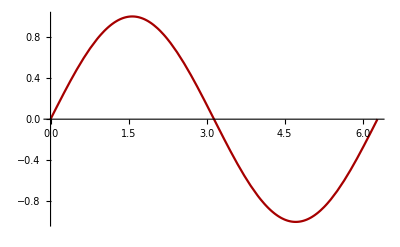

```mathematica
Plot[Sin[x],{x,0,2 π}] (* 2D plot - Sinx vs. x, y=sinx *)
```

```mathematica
Plot3D[x^4+y^4,{x,-100,100},{y,-100,100}] (* 3D plot : Z=x^2+y^2 *)
```

-Graphics3D-

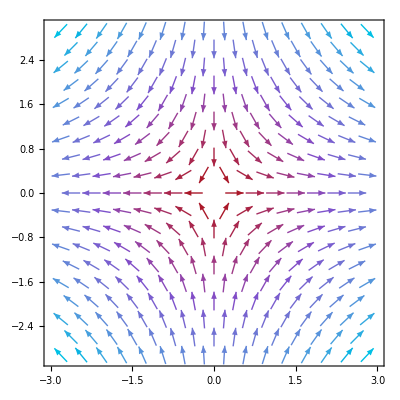

```mathematica
VectorPlot[{x,-y},{x,-3,3},{y,-3,3}] (* Vector plot : V=xi-yj *)
```

2D plots → motion, waves
3D plots → potentials, energy landscapes
Vector plots → electric fields, fluid flow, forces

Interactive Notebooks

A Mathematica notebook is a live document where: (i) Text (ii) Equations (iii) Code (iv) Plots etc.. all coexist and update together.

```mathematica
f[x_]:=x^3
g[y_]:=y^2  (* define function *)
```

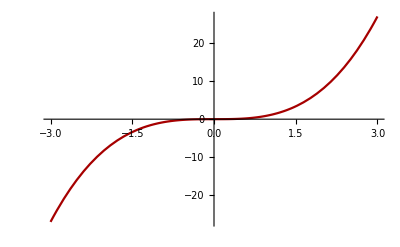

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
D[f[x],x]
```

3 x^2

```mathematica
Integrate[f[x],x]
```

x^4/4

```mathematica
NIntegrate[g[z^3],{z,0,1}]
```

0.142857

```mathematica
NIntegrate[g[z^2],{z,0,1}]
```

0.2

In summary, Mathematica allows us to
• Compute exactly (symbolic)
• Compute approximately (numerical)
• Visualize physics geometrically
• Combine code, math, and explanation in one notebook

## 2. Function Behaviour Near Extrema

Finding Derivatives

```mathematica
f[x_]:=x^3-3 x^2+2;
```

```mathematica
f[2]
```

-2

```mathematica
D[f[x],x]
```

-6 x+3 x^2

```mathematica
D[D[f[x],x],x]
```

-6+6 x

```mathematica
D[f[x],x]/.{x->2}
```

0

```mathematica
D[D[f[x],x],x]/.{x->2}
```

6

Finding Critical Points

```mathematica
Solve[D[f[x],x]==0,x]
```

{{x→0},{x→2}}

```mathematica
Solve[-6 x+3 x^2==0,x]
```

{{x→0},{x→2}}

Visualizing Extrema

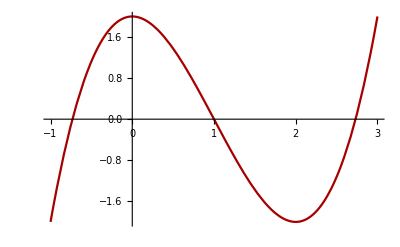

```mathematica
Plot[f[x],{x,-1,3}]
```

Taylor Expansion Near an Extremum

```mathematica
Series[f[x],{x,2,6}] (* around the point x=2, keeping terms up to 2nd order *)
```

-2+3 (x-2)^2+(x-2)^3+O[x-2]^7

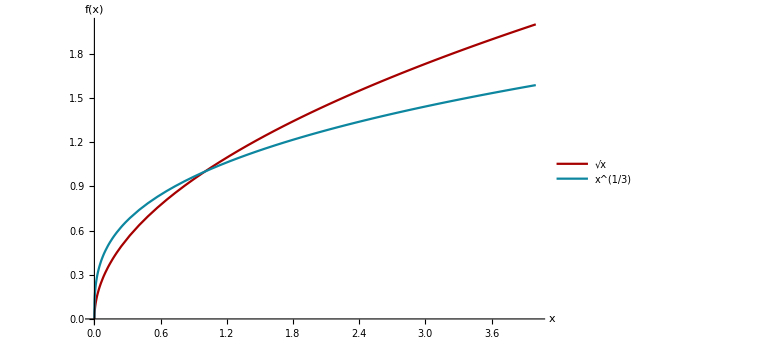

```mathematica
Plot[{Sqrt[x],x^(1/3)},{x,0,4},PlotLegends->{Sqrt[x],x^(1/3)},AxesLabel->{Style["x",20,Black],Style["f(x)",20,Black]},PlotStyle->Thick,AxesStyle->Thick,TicksStyle->12,ImageSize->Large]
```

```mathematica
Solve[Sqrt[x]==x^(1/3),x]
```

{{x→0},{x→1}}

```mathematica
Solve[x^(1/3)==Log[x],x] (* x^(1/3)-Log[x]=0 *)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-27 ProductLog[-1/3]^3},{x→-27 ProductLog[-1,-1/3]^3}}

Hence, this equation has no closed-form solution, use numerical solving:

```mathematica
NSolve[x^(1/3)==Log[x],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→6.40567},{x→93.3545}}

Here, (i) x^(1/3) is a multivalued inverse power (ii) Log[x] has domain restrictions (x>0)
To solve numerically, NSolve[] internally uses inverse operations like:
• Raising both sides to powers
• Applying exponentials
These steps can lose solutions or restrict domains.

```mathematica
N[Reduce[x^(1/3)==Log[x],x,Reals]]
```

x==6.40567||x==93.3545

To explicitly get the smallest positive solution:

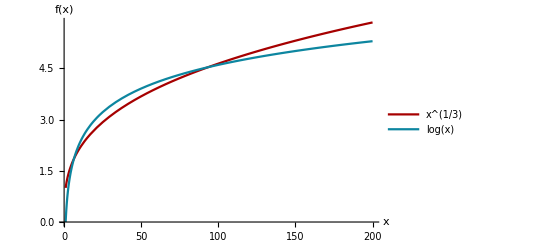

```mathematica
Plot[{x^(1/3),Log[x]},{x,1,200},PlotLegends->{x^(1/3),Log[x]},AxesLabel->{Style["x",20,Black],Style["f(x)",20,Black]},PlotStyle->Thick]
```

```mathematica
x/. FindRoot[x^(1/3)==Log[x],{x,90}]
```

93.3545

Zeros of Functions

```mathematica
Solve[x^2-4==0,x]
```

{{x→-2},{x→2}}

```mathematica
f[x_]:=x^2-4;
```

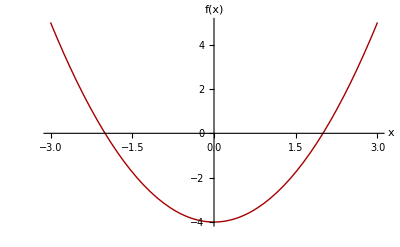

```mathematica
Plot[f[x],{x,-3,3},AxesLabel->{Style["x",20,Black],Style["f(x)",20,Black]},PlotStyle->Thick]
```

```mathematica
Solve[f[x]==-4,x]
```

{{x→0},{x→0}}

Asymptotic Behaviour

```mathematica
Limit[1/x,x->Infinity]
```

0

```mathematica
f[x_]:=0.5+0.2 Exp[-0.5 x] Sin[3 x];
```

```mathematica
Limit[f[x],x->Infinity]
```

0.5

```mathematica
Limit[1-Exp[-x],x->Infinity]
```

1

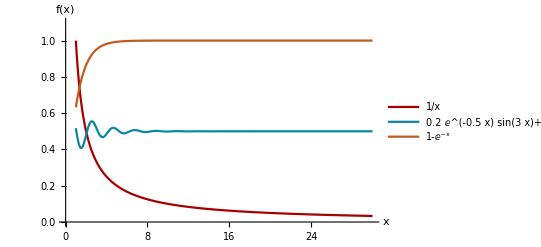

```mathematica
Plot[{1/x,f[x],1-Exp[-x]},{x,1,30},PlotLegends->{1/x,0.5+0.2 Exp[-0.5 x] Sin[3 x],1-Exp[-x]},AxesLabel->{Style["x",20,Black],Style["f(x)",20,Black]},PlotRange->{0,1.1},PlotStyle->Thick]
```

```mathematica
Limit[ArcTanh[x],x->1,Direction->"FromAbove"]
```

∞

```mathematica
Limit[ArcTanh[x],x->-1,Direction->"FromBelow"]
```

-∞

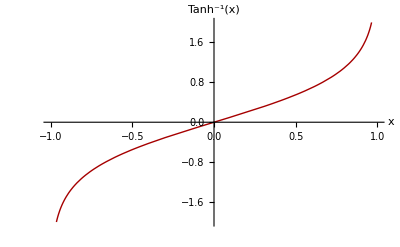

```mathematica
Plot[ArcTanh[x],{x,-5,5},PlotRange->{-2,2},AxesLabel->{Style[TraditionalForm[x],20,Black],Style[TraditionalForm@Superscript[Tanh,-1][x],20,Black]},PlotStyle->Thick]
```

Problem-1:

For the function,   f(r)=e^(-r/2)√(1+r)Sin(3r) ,  with   r>0.
  (i)  Find the zeros of   f(r).
 (ii)  Show that the distance between two consecutive zeros is constant.
(iii)  Compute this distance.

```mathematica
f[r_]:=Exp[-r/2] Sqrt[1+r] Sin[3r];
```

```mathematica
Solve[Sin[3r]==0,r]
```

{{r→ConditionalExpression[(2 π C[1])/3, C[1]∈ℤ]},{r→ConditionalExpression[1/3 (π+2 π C[1]), C[1]∈ℤ]}}

```mathematica
r[n_]:=2n Pi/3;
```

```mathematica
Simplify[r[n+1]-r[n]]
```

(2 π)/3

```mathematica
Limit[r[n+1]-r[n],n->Infinity]
```

(2 π)/3

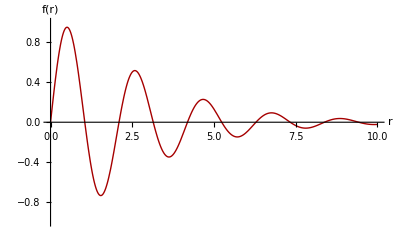

```mathematica
Plot[f[r],{r,0,10},PlotRange->{-1,1},AxesLabel->{Style["r",20,Black],Style["f(r)",20,Black]},PlotStyle->Thick]
```

```mathematica
f[r_]:=Exp[-r/2] Sqrt[1+r] Sin[r^2];
```

```mathematica
Solve[Sin[r^2]==0,r]
```

{{r→ConditionalExpression[-√(2 π) √C[1], C[1]∈ℤ]},{r→ConditionalExpression[√(2 π) √C[1], C[1]∈ℤ]},{r→ConditionalExpression[-√(π+2 π C[1]), C[1]∈ℤ]},{r→ConditionalExpression[√(π+2 π C[1]), C[1]∈ℤ]}}

```mathematica
R[n_]:=√(2 π) √n; (*only +ve root consider *)
```

```mathematica
Simplify[R[n+1]-R[n]]
```

(-√n+√(1+n)) √(2 π)

```mathematica
N[Simplify[R[4]-R[3]]]
```

0.671649

```mathematica
N[Simplify[R[200]-R[199]]]
```

0.0887337

```mathematica
Series[Sqrt[n+1]-Sqrt[n],{n,Infinity,1}]
```

(√(1/n))/2+O[1/n]^(3/2)

```mathematica
Limit[R[n+1]-R[n],n->Infinity]
```

0

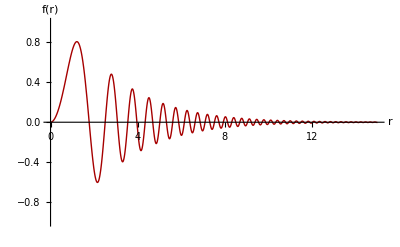

```mathematica
Plot[f[r],{r,0,15},PlotRange->{-1,1},AxesLabel->{Style["r",20,Black],Style["f(r)",20,Black]},PlotStyle->Thick]
```

## 3. Plotting Simple Functions

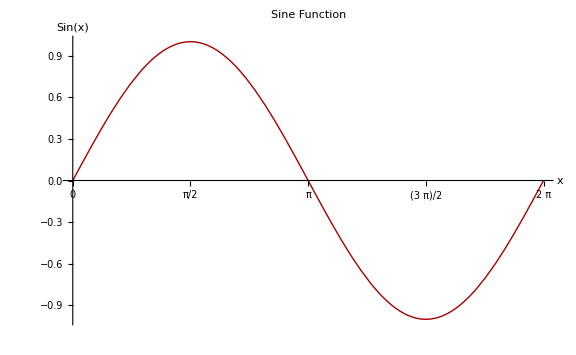

```mathematica
Plot[Sin[x],{x,0,2 Pi},AxesLabel->{Style["x",20,Black],Style["Sin(x)",20,Black]},PlotLabel->Style["Sine Function",16,Bold],Ticks->{Range[0,2 Pi,Pi/2],Automatic},TicksStyle->20,AxesStyle->Thick,PlotStyle->Thick,ImageSize->Large]
```

Vector Fields and Visualization

```mathematica
v[x_,y_]:={x^2,-y^2}  (* defining a vector field *)
```

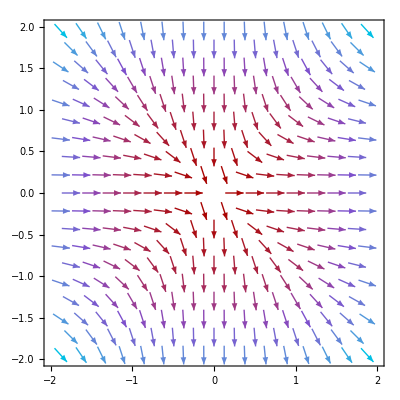

```mathematica
VectorPlot[v[x,y],{x,-2,2},{y,-2,2}]
```

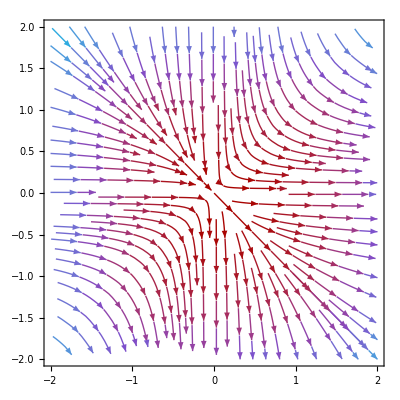

```mathematica
StreamPlot[v[x,y],{x,-2,2},{y,-2,2}]  (* Streamline plot *)
```

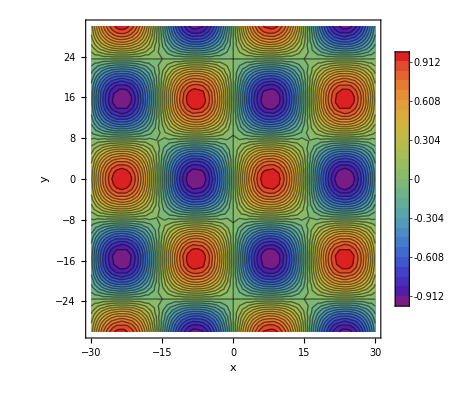

```mathematica
ContourPlot[Sin[0.2 x] Cos[0.2 y],{x,-30,30},{y,-30,30},Contours->25,ColorFunction->"Rainbow",ColorFunctionScaling->True,FrameLabel->{Style["x",20,Black],Style["y",20,Black]},PlotLegends->Automatic,ContourShading->True] (*Z=Sin[0.2 x] Cos[0.2 y]*)
```

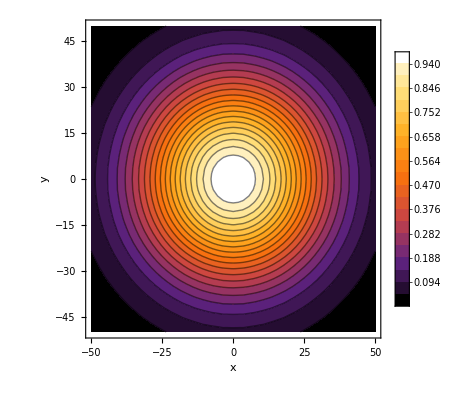

```mathematica
ContourPlot[Exp[-0.001 (x^2+y^2)],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"SunsetColors",ColorFunctionScaling->True,FrameLabel->{Style["x",20,Black],Style["y",20,Black]},PlotLegends->Automatic,ContourShading->True]
```

## 4. A Simple Problem

Let’s consider a radioactive element that decays over time. At time t=0, the amount of element present is 
N_0, and no decay has occurred. As time increases, the radioactive decay of the element is given by the equation 

                                                           N_f = N_0 e^-λt

where  λ=ln2/t_(1/2) = 1.1×10^-2 s^-1 and N_f is the number of remaining element, t is the time elapsed, and t_(1/2) is the half-life of the element.  Calculates the amount of element remaining after a given time t.

```mathematica
N0=100.0;  (* initial amount of the element in kg. *)
time=100;  (* Decay time in seconds. *)
Lambda= 1.1*10^(-2); (* Decay constant in s^(-1) *)
Nf=N0 Exp[-Lambda time];
```

```mathematica
Print["Remaining element after ",time," second is: ",Nf, "kg."]
```

Remaining element after 100 second is: 33.2871kg.

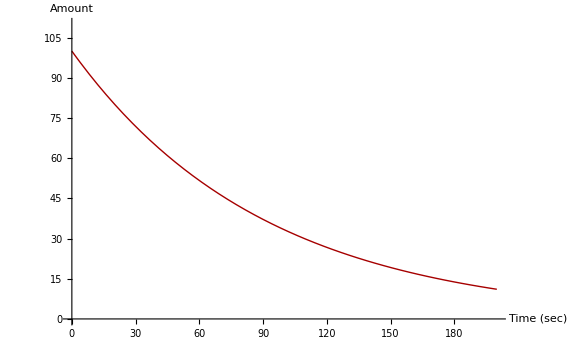

```mathematica
Plot[N0 Exp[-Lambda time],{time,0,200},PlotRange->{0,110},AxesLabel->{Style["Time (sec)",16,Black],Style["Amount",16,Black]},TicksStyle->12,AxesStyle->Thick,PlotStyle->Thick,ImageSize->Large]
```